2.338028044119034×10^6

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 10000 iterations.

2.338028045983369×10^6

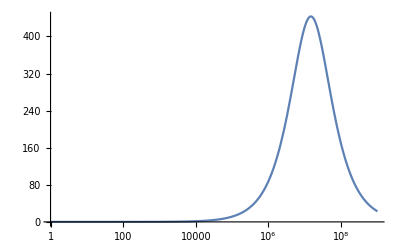

```mathematica
Q=3.416*10^-10;
R=1037.9;
n=0.9;
NumberForm[1/(R*Q)^(1/n)/2/Pi,20]
res =NMaximize[{(Q w^n Sin[(n π)/2])/((1/R+Q w^n Cos[(n π)/2])^2+Q^2 w^(2 n) Sin[(n π)/2]^2),w>0},w,AccuracyGoal->20,PrecisionGoal->18,MaxIterations->10000];
NumberForm[w/2/Pi/.res[[2]],20]
LogLinearPlot[(Q w^n Sin[(n π)/2])/((1/R+Q w^n Cos[(n π)/2])^2+Q^2 w^(2 n) Sin[(n π)/2]^2),{w,1,10^9}, PlotRange->All]
```

```mathematica
NumberForm[( 1/R+Q(I*w)^n)^-1/.w->4Pi,9]
1/(R ((1/R+Q w^n Cos[(n π)/2])^2+Q^2 w^(2 n) Sin[(n π)/2]^2))+(Q w^n Cos[(n π)/2])/((1/R+Q w^n Cos[(n π)/2])^2+Q^2 w^(2 n) Sin[(n π)/2]^2)/.w->4Pi
-(ⅈ Q w^n Sin[(n π)/2])/((1/R+Q w^n Cos[(n π)/2])^2+Q^2 w^(2 n) Sin[(n π)/2]^2)/.w->4Pi
```

1037.89944-0.00354598767 ⅈ

1037.9

0.-0.00354599 ⅈ

```mathematica
Module[{R,Q,w,n},Refine[ComplexExpand[(1/R+Q*(I*w)^n)^-1],{Element[R,Reals],Element[n,Integers],Element[w,Integers],Element[Q,Integers], w>0}]]
```

1/(R$2329 ((1/R$2329+Q$2329 w$2329^n$2329 Cos[(n$2329 π)/2])^2+Q$2329^2 w$2329^(2 n$2329) Sin[(n$2329 π)/2]^2))+(Q$2329 w$2329^n$2329 Cos[(n$2329 π)/2])/((1/R$2329+Q$2329 w$2329^n$2329 Cos[(n$2329 π)/2])^2+Q$2329^2 w$2329^(2 n$2329) Sin[(n$2329 π)/2]^2)-(ⅈ Q$2329 w$2329^n$2329 Sin[(n$2329 π)/2])/((1/R$2329+Q$2329 w$2329^n$2329 Cos[(n$2329 π)/2])^2+Q$2329^2 w$2329^(2 n$2329) Sin[(n$2329 π)/2]^2)